```mathematica
NFW[x_]:=Piecewise[{{1/(x^2-1)(1-2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))]), x≤ 1}, {1/(x^2-1)(1-2/(√(x^2-1))ArcTan[√((x-1)/(1+x))]), x>1}}]
MNFW[x_]:=Log[x/2]+Piecewise[{{2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))], x≤1}, {2/(√(x^2-1))ArcTan[√((x-1)/(1+x))], x>1}}]
```

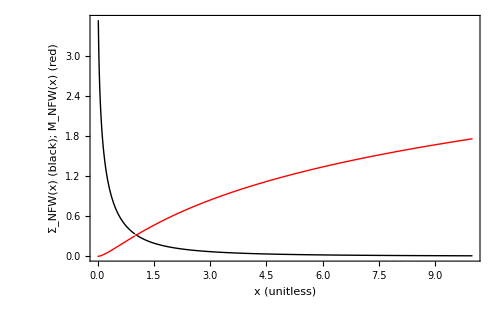

```mathematica
Plot[{NFW[x],MNFW[x]},{x,0,10},Frame->True,PlotStyle->{{Black,Thick},{Red, Thick}},FrameLabel->{"x (unitless)","Σ_NFW(x) (black); M_NFW(x) (red)","NFW Profile and Enclosed Mass at Normalized Scale" },LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18], ImageSize->500]
```

```mathematica
Integrate[NFW[R/r]R,{R,0,Rprime},Assumptions->Element[Rprime,Reals]&&Rprime>0]
```

```mathematica
Integrate[NFW[r x]x,{x,0,Rprime},Assumptions->Element[Rprime,Reals]&&Rprime>0]
```

```mathematica
Integrate[NFW[R]R,{R,0,x},Assumptions->Element[x,Reals]&&x>0]//FullSimplify
```

```mathematica
MNFW2[x_]:=Piecewise[{{2 √(1/(1-x^2)) ArcTanh[1/(√((1+x)/(1-x)))]+Log[x/2], x≤1}, {(2 ArcTan[√((-1+x)/(1+x))])/(√(-1+x^2))+Log[x/2], True}}]
```

```mathematica
MNFW3[x_]:=Log[x/2]+2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))]
```

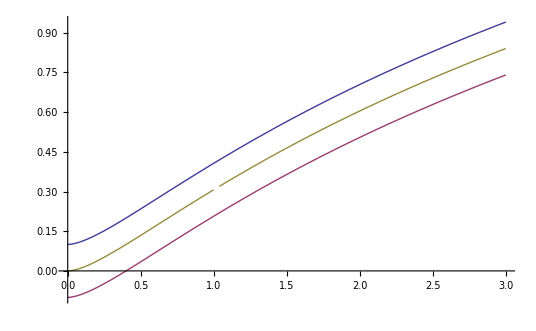

```mathematica
Plot[{2 √(1/(1-x^2)) ArcTanh[1/(√((1+x)/(1-x)))]+Log[x/2]+0.1,(2 ArcTan[√((-1+x)/(1+x))])/(√(-1+x^2))+Log[x/2]-0.1, MNFW2[x]},{x,0,3}]
```

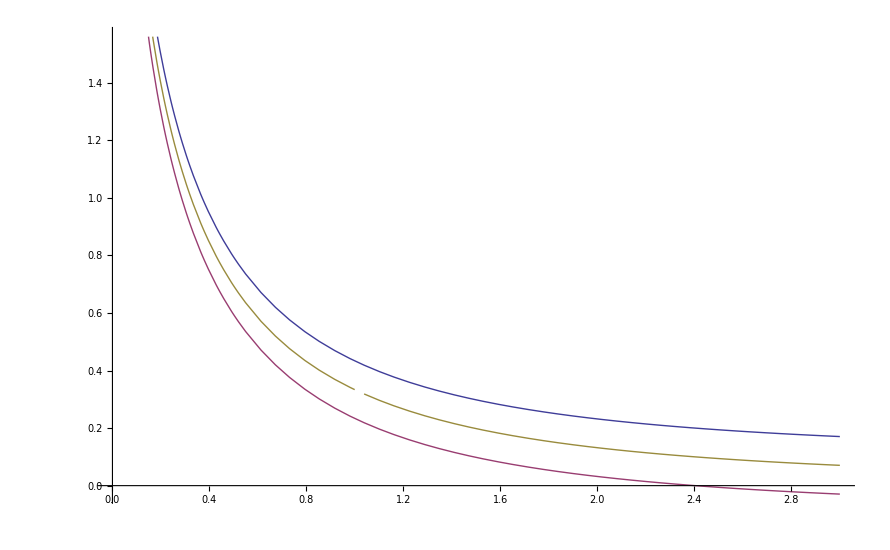

```mathematica
Plot[{1/(x^2-1)(1-2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))])+0.1,1/(x^2-1)(1-2/(√(x^2-1))ArcTan[√((x-1)/(1+x))])-0.1,NFW[x]},{x,0,3}]
```

```mathematica
f[x_]:=1/(x^2-1)(1-2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))])
```

```mathematica
MNFW3[x_]:=Log[x/2]+2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))]
PxPerRad=180/π 3600/0.03;
rs[M200_,c_]:=N[(4.302/67.8^2*10^3)^(1/3),10]*(M200)^(1/3)/c
N[(4.302/67.8^2*10^3)^(1/3),10]
rad[px_]:=(180/π 3600/0.03)^-1 px
ΩM=0.315;
ΩD=0.685;
ZEQ=3391;
H0=4424.778 ;
AngDiDist[z1_,z2_]:=H0/(z2+1)NIntegrate[1/(√(ΩM(1+z/ZEQ)z^3+ΩD)),{z,z1+1,z2+1}]

Dl=AngDiDist[0,0.3]
G=4.302;
deltac2[c_]:=1/(Log[1+c]-c/(1+c))
NFWPrefactor[M200_,c_]:=(PxPerRad*4*G*M200 *deltac2[c])/(9*Dl*10^5)
Alpha[px_,M200_,c_]:=NFWPrefactor[M200,c] MNFW3[rad[px] Dl/rs[M200,c]]/(rad[px]*px)
```

0.978146

946.088

```mathematica
FindRoot[Alpha[x,20,2]==0.22,{x,150}]
```

{x→5909.24}

```mathematica
Alpha[1000,20,2]
```

0.589113

```mathematica
rs[2,4]*4/Dl
rs[5,4]*4/Dl
rs[10,4]*4/Dl
rs[20,4]*4/Dl
```

0.00130261

0.00176792

0.00222744

0.00280639